```mathematica
Clear["Global`*"]
Ca=10^-17;
e=1.602* 10^-19;
EC=e^2/(2*Ca);
kb=1.38* 10^-23;
gamma=1000000000;
g=2.002319;
muB=9.27400* 10^-24;
B=20;
deltaEb=B*muB*g;
alphag=1/20 ;
T=4;
muL=e*V/2;
muR=e*-V/2;
mu111=Vg*e*alphag;
mu121=Vg*e*alphag+deltaEb;
mu212=Vg*e*alphag+EC;
mu211=Vg*e*alphag+EC+deltaEb;

f[mu1_,mu2_,T_]:=1/(Exp[(mu1-mu2)/(kb*T)]+1);

W1101={f[mu111,muL,T],f[mu111,muR,T]};
W1201={f[mu121,muL,T],f[mu121,muR,T]};
W2112={f[mu212,muL,T],f[mu212,muR,T]};
W2111={f[mu211,muL,T],f[mu211,muR,T]};
W0111={1-f[mu111,muL,T],1-f[mu111,muR,T]};
W0112={1-f[mu121,muL,T],1-f[mu121,muR,T]};
W1121={1-f[mu211,muL,T],1-f[mu211,muR,T]};
W1221={1-f[mu212,muL,T],1-f[mu212,muR,T]};

WMAT={{1,1,1,1},{Total[W1101],-Total[W0111]-Total[W2111],0,Total[W1121]},{Total[W1201],0,-Total[W0112]-Total[W2112],Total[W1221]},{0,Total[W2111],Total[W2112],-Total[W1121]-Total[W1221]}};
R={1,0,0,0};
P=LinearSolve[WMAT,R];
IL=-e*gamma*(-W0111[[1]]*P[[2]]-W0112[[1]]*P[[3]]+W1101[[1]]*P[[1]]-W1121[[1]]*P[[4]]+W1201[[1]]*P[[1]]-W1221[[1]]*P[[4]]+W2111[[1]]*P[[2]]+W2112[[1]]*P[[3]]);
CON=N[D[IL,V]];

PM=DiscreteMarkovProcess[R,WMAT];
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

```mathematica
W=W0111/.V->0.02
W/.Vg->0.03 //MatrixForm
```

{1-1/(1+ⅇ^(1.81159×10^22 (-1.602×10^-21+8.01×10^-21 Vg))),1-1/(1+ⅇ^(1.81159×10^22 (1.602×10^-21+8.01×10^-21 Vg)))}

(1.93472×10^-11
1.)

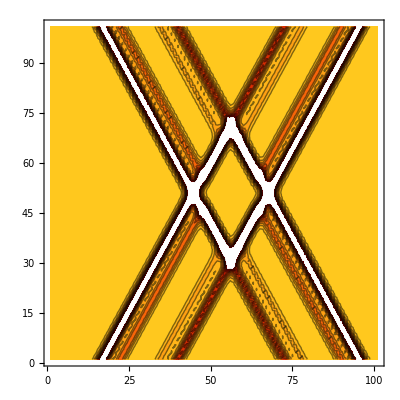

```mathematica
ListContourPlot[Table[CON,{V,-0.025,0.025,0.0005},{Vg,-0.6,0.3,0.009}],ColorFunction->"Warm"]
```

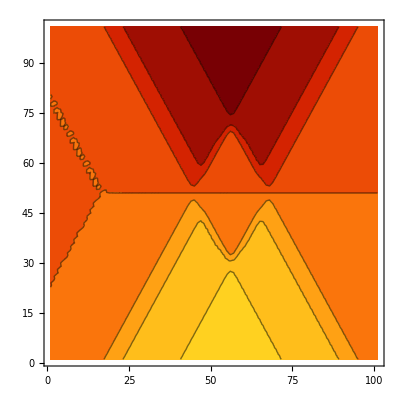

```mathematica
ListContourPlot[Table[IL,{V,-0.025,0.025,0.0005},{Vg,-0.6,0.3,0.009}],ColorFunction->"Warm"]
```

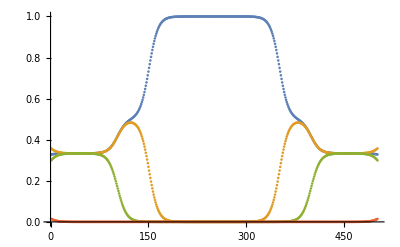

```mathematica
PN=P/.Vg->0.1;
ListPlot[Table[Table[PN[[i]],{V,-0.025,0.025,0.0001}],{i,1,4}]]
```

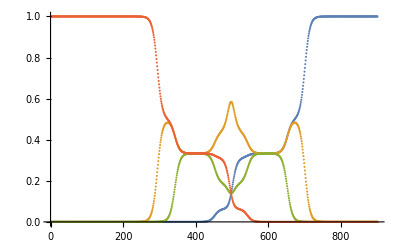

```mathematica
PN=P/.V->0.01;
ListPlot[Table[Table[PN[[i]],{Vg,-0.6,0.3,0.001}],{i,1,4}]]
```